```mathematica
Clear[e,c,hbar,me]
```

```mathematica
(* SO(14)/G_2/D_6  magnetic quantum gravity model*)
(* magnetic velocity is v=c/6 from continuity of the real D_6 model S0(12) over {t,tau} time to give a SO(14) matrix group*)
(*5 dimensional Lepton projected on 3 dimenaions gives the 5/3 scaling factor*)
```

```mathematica
Au1=(5/3)*Table[If[i==j,0,If[Mod[i+j,2]==0,e/r,-(v/c)e/r]],{i,14},{j,14}]
```

{{0,-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r)},{-(5 e v)/(3 c r),0,-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r)},{(5 e)/(3 r),-(5 e v)/(3 c r),0,-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r)},{-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),0,-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r)},{(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),0,-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r)},{-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),0,-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r)},{(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),0,-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r)},{-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),0,-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r)},{(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),0,-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r)},{-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),0,-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r)},{(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),0,-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r)},{-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),0,-(5 e v)/(3 c r),(5 e)/(3 r)},{(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),0,-(5 e v)/(3 c r)},{-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),0}}

```mathematica
Au2=(5/3)*Table[If[i==j,0,If[Mod[i+j,2]==0,-e/r,(v/c)*e/r]],{i,14},{j,14}]
```

{{0,(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r)},{(5 e v)/(3 c r),0,(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r)},{-(5 e)/(3 r),(5 e v)/(3 c r),0,(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r)},{(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),0,(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r)},{-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),0,(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r)},{(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),0,(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r)},{-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),0,(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r)},{(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),0,(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r)},{-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),0,(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r)},{(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),0,(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r)},{-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),0,(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r)},{(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),0,(5 e v)/(3 c r),-(5 e)/(3 r)},{-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),0,(5 e v)/(3 c r)},{(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),0}}

```mathematica
Au3=Table[If[i>j,Au1[[i,j]],0],{i,14},{j,14}]
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-(5 e v)/(3 c r),0,0,0,0,0,0,0,0,0,0,0,0,0},{(5 e)/(3 r),-(5 e v)/(3 c r),0,0,0,0,0,0,0,0,0,0,0,0},{-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),0,0,0,0,0,0,0,0,0,0,0},{(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),0,0,0,0,0,0,0,0,0,0},{-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),0,0,0,0,0,0,0,0,0},{(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),0,0,0,0,0,0,0,0},{-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),0,0,0,0,0,0,0},{(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),0,0,0,0,0,0},{-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),0,0,0,0,0},{(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),0,0,0,0},{-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),0,0,0},{(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),0,0},{-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),0}}

```mathematica
Au4=Table[If[i<j,Au2[[i,j]],0],{i,14},{j,14}]
```

{{0,(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r)},{0,0,(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r)},{0,0,0,(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r)},{0,0,0,0,(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r)},{0,0,0,0,0,(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r)},{0,0,0,0,0,0,(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r)},{0,0,0,0,0,0,0,(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r)},{0,0,0,0,0,0,0,0,(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r)},{0,0,0,0,0,0,0,0,0,(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r)},{0,0,0,0,0,0,0,0,0,0,(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r)},{0,0,0,0,0,0,0,0,0,0,0,(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r)},{0,0,0,0,0,0,0,0,0,0,0,0,(5 e v)/(3 c r),-(5 e)/(3 r)},{0,0,0,0,0,0,0,0,0,0,0,0,0,(5 e v)/(3 c r)},{0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
(*SO(14) field, half electric half magnetic anti-symmetric matrix*)
```

```mathematica
Au=Au3+Au4
```

{{0,(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r)},{-(5 e v)/(3 c r),0,(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r)},{(5 e)/(3 r),-(5 e v)/(3 c r),0,(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r)},{-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),0,(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r)},{(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),0,(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r)},{-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),0,(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r)},{(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),0,(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r)},{-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),0,(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r)},{(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),0,(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r)},{-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),0,(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r)},{(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),0,(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r)},{-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),0,(5 e v)/(3 c r),-(5 e)/(3 r)},{(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),0,(5 e v)/(3 c r)},{-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),0}}

```mathematica
Aut=Transpose[Au]
```

{{0,-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r)},{(5 e v)/(3 c r),0,-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r)},{-(5 e)/(3 r),(5 e v)/(3 c r),0,-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r)},{(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),0,-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r)},{-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),0,-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r)},{(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),0,-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r)},{-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),0,-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r)},{(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),0,-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r)},{-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),0,-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r)},{(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),0,-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r),(5 e)/(3 r)},{-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),0,-(5 e v)/(3 c r),(5 e)/(3 r),-(5 e v)/(3 c r)},{(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),0,-(5 e v)/(3 c r),(5 e)/(3 r)},{-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),0,-(5 e v)/(3 c r)},{(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),-(5 e)/(3 r),(5 e v)/(3 c r),0}}

```mathematica
(*energy squared field scaled by 1/alpha: E^2=(1/α)^2*Fuv.Fuvt/14*)
```

```mathematica
Fuv=ExpandAll[(hbar*c/e^2)^2*(e*Au).(e*Aut)]/14
```

{{1/14 ((50 c^2 hbar^2)/(3 r^2)+(175 hbar^2 v^2)/(9 r^2)),-(50 c hbar^2 v)/(21 r^2),1/14 ((125 c^2 hbar^2)/(9 r^2)+(125 hbar^2 v^2)/(9 r^2)),-(100 c hbar^2 v)/(63 r^2),1/14 ((25 c^2 hbar^2)/(3 r^2)+(25 hbar^2 v^2)/(3 r^2)),-(50 c hbar^2 v)/(63 r^2),1/14 ((25 c^2 hbar^2)/(9 r^2)+(25 hbar^2 v^2)/(9 r^2)),0,1/14 (-(25 c^2 hbar^2)/(9 r^2)-(25 hbar^2 v^2)/(9 r^2)),(50 c hbar^2 v)/(63 r^2),1/14 (-(25 c^2 hbar^2)/(3 r^2)-(25 hbar^2 v^2)/(3 r^2)),(100 c hbar^2 v)/(63 r^2),1/14 (-(125 c^2 hbar^2)/(9 r^2)-(125 hbar^2 v^2)/(9 r^2)),(50 c hbar^2 v)/(21 r^2)},{-(50 c hbar^2 v)/(21 r^2),1/14 ((50 c^2 hbar^2)/(3 r^2)+(175 hbar^2 v^2)/(9 r^2)),-(50 c hbar^2 v)/(21 r^2),1/14 ((125 c^2 hbar^2)/(9 r^2)+(125 hbar^2 v^2)/(9 r^2)),-(100 c hbar^2 v)/(63 r^2),1/14 ((25 c^2 hbar^2)/(3 r^2)+(25 hbar^2 v^2)/(3 r^2)),-(50 c hbar^2 v)/(63 r^2),1/14 ((25 c^2 hbar^2)/(9 r^2)+(25 hbar^2 v^2)/(9 r^2)),0,1/14 (-(25 c^2 hbar^2)/(9 r^2)-(25 hbar^2 v^2)/(9 r^2)),(50 c hbar^2 v)/(63 r^2),1/14 (-(25 c^2 hbar^2)/(3 r^2)-(25 hbar^2 v^2)/(3 r^2)),(100 c hbar^2 v)/(63 r^2),1/14 (-(125 c^2 hbar^2)/(9 r^2)-(125 hbar^2 v^2)/(9 r^2))},{1/14 ((125 c^2 hbar^2)/(9 r^2)+(125 hbar^2 v^2)/(9 r^2)),-(50 c hbar^2 v)/(21 r^2),1/14 ((50 c^2 hbar^2)/(3 r^2)+(175 hbar^2 v^2)/(9 r^2)),-(50 c hbar^2 v)/(21 r^2),1/14 ((125 c^2 hbar^2)/(9 r^2)+(125 hbar^2 v^2)/(9 r^2)),-(100 c hbar^2 v)/(63 r^2),1/14 ((25 c^2 hbar^2)/(3 r^2)+(25 hbar^2 v^2)/(3 r^2)),-(50 c hbar^2 v)/(63 r^2),1/14 ((25 c^2 hbar^2)/(9 r^2)+(25 hbar^2 v^2)/(9 r^2)),0,1/14 (-(25 c^2 hbar^2)/(9 r^2)-(25 hbar^2 v^2)/(9 r^2)),(50 c hbar^2 v)/(63 r^2),1/14 (-(25 c^2 hbar^2)/(3 r^2)-(25 hbar^2 v^2)/(3 r^2)),(100 c hbar^2 v)/(63 r^2)},{-(100 c hbar^2 v)/(63 r^2),1/14 ((125 c^2 hbar^2)/(9 r^2)+(125 hbar^2 v^2)/(9 r^2)),-(50 c hbar^2 v)/(21 r^2),1/14 ((50 c^2 hbar^2)/(3 r^2)+(175 hbar^2 v^2)/(9 r^2)),-(50 c hbar^2 v)/(21 r^2),1/14 ((125 c^2 hbar^2)/(9 r^2)+(125 hbar^2 v^2)/(9 r^2)),-(100 c hbar^2 v)/(63 r^2),1/14 ((25 c^2 hbar^2)/(3 r^2)+(25 hbar^2 v^2)/(3 r^2)),-(50 c hbar^2 v)/(63 r^2),1/14 ((25 c^2 hbar^2)/(9 r^2)+(25 hbar^2 v^2)/(9 r^2)),0,1/14 (-(25 c^2 hbar^2)/(9 r^2)-(25 hbar^2 v^2)/(9 r^2)),(50 c hbar^2 v)/(63 r^2),1/14 (-(25 c^2 hbar^2)/(3 r^2)-(25 hbar^2 v^2)/(3 r^2))},{1/14 ((25 c^2 hbar^2)/(3 r^2)+(25 hbar^2 v^2)/(3 r^2)),-(100 c hbar^2 v)/(63 r^2),1/14 ((125 c^2 hbar^2)/(9 r^2)+(125 hbar^2 v^2)/(9 r^2)),-(50 c hbar^2 v)/(21 r^2),1/14 ((50 c^2 hbar^2)/(3 r^2)+(175 hbar^2 v^2)/(9 r^2)),-(50 c hbar^2 v)/(21 r^2),1/14 ((125 c^2 hbar^2)/(9 r^2)+(125 hbar^2 v^2)/(9 r^2)),-(100 c hbar^2 v)/(63 r^2),1/14 ((25 c^2 hbar^2)/(3 r^2)+(25 hbar^2 v^2)/(3 r^2)),-(50 c hbar^2 v)/(63 r^2),1/14 ((25 c^2 hbar^2)/(9 r^2)+(25 hbar^2 v^2)/(9 r^2)),0,1/14 (-(25 c^2 hbar^2)/(9 r^2)-(25 hbar^2 v^2)/(9 r^2)),(50 c hbar^2 v)/(63 r^2)},{-(50 c hbar^2 v)/(63 r^2),1/14 ((25 c^2 hbar^2)/(3 r^2)+(25 hbar^2 v^2)/(3 r^2)),-(100 c hbar^2 v)/(63 r^2),1/14 ((125 c^2 hbar^2)/(9 r^2)+(125 hbar^2 v^2)/(9 r^2)),-(50 c hbar^2 v)/(21 r^2),1/14 ((50 c^2 hbar^2)/(3 r^2)+(175 hbar^2 v^2)/(9 r^2)),-(50 c hbar^2 v)/(21 r^2),1/14 ((125 c^2 hbar^2)/(9 r^2)+(125 hbar^2 v^2)/(9 r^2)),-(100 c hbar^2 v)/(63 r^2),1/14 ((25 c^2 hbar^2)/(3 r^2)+(25 hbar^2 v^2)/(3 r^2)),-(50 c hbar^2 v)/(63 r^2),1/14 ((25 c^2 hbar^2)/(9 r^2)+(25 hbar^2 v^2)/(9 r^2)),0,1/14 (-(25 c^2 hbar^2)/(9 r^2)-(25 hbar^2 v^2)/(9 r^2))},{1/14 ((25 c^2 hbar^2)/(9 r^2)+(25 hbar^2 v^2)/(9 r^2)),-(50 c hbar^2 v)/(63 r^2),1/14 ((25 c^2 hbar^2)/(3 r^2)+(25 hbar^2 v^2)/(3 r^2)),-(100 c hbar^2 v)/(63 r^2),1/14 ((125 c^2 hbar^2)/(9 r^2)+(125 hbar^2 v^2)/(9 r^2)),-(50 c hbar^2 v)/(21 r^2),1/14 ((50 c^2 hbar^2)/(3 r^2)+(175 hbar^2 v^2)/(9 r^2)),-(50 c hbar^2 v)/(21 r^2),1/14 ((125 c^2 hbar^2)/(9 r^2)+(125 hbar^2 v^2)/(9 r^2)),-(100 c hbar^2 v)/(63 r^2),1/14 ((25 c^2 hbar^2)/(3 r^2)+(25 hbar^2 v^2)/(3 r^2)),-(50 c hbar^2 v)/(63 r^2),1/14 ((25 c^2 hbar^2)/(9 r^2)+(25 hbar^2 v^2)/(9 r^2)),0},{0,1/14 ((25 c^2 hbar^2)/(9 r^2)+(25 hbar^2 v^2)/(9 r^2)),-(50 c hbar^2 v)/(63 r^2),1/14 ((25 c^2 hbar^2)/(3 r^2)+(25 hbar^2 v^2)/(3 r^2)),-(100 c hbar^2 v)/(63 r^2),1/14 ((125 c^2 hbar^2)/(9 r^2)+(125 hbar^2 v^2)/(9 r^2)),-(50 c hbar^2 v)/(21 r^2),1/14 ((50 c^2 hbar^2)/(3 r^2)+(175 hbar^2 v^2)/(9 r^2)),-(50 c hbar^2 v)/(21 r^2),1/14 ((125 c^2 hbar^2)/(9 r^2)+(125 hbar^2 v^2)/(9 r^2)),-(100 c hbar^2 v)/(63 r^2),1/14 ((25 c^2 hbar^2)/(3 r^2)+(25 hbar^2 v^2)/(3 r^2)),-(50 c hbar^2 v)/(63 r^2),1/14 ((25 c^2 hbar^2)/(9 r^2)+(25 hbar^2 v^2)/(9 r^2))},{1/14 (-(25 c^2 hbar^2)/(9 r^2)-(25 hbar^2 v^2)/(9 r^2)),0,1/14 ((25 c^2 hbar^2)/(9 r^2)+(25 hbar^2 v^2)/(9 r^2)),-(50 c hbar^2 v)/(63 r^2),1/14 ((25 c^2 hbar^2)/(3 r^2)+(25 hbar^2 v^2)/(3 r^2)),-(100 c hbar^2 v)/(63 r^2),1/14 ((125 c^2 hbar^2)/(9 r^2)+(125 hbar^2 v^2)/(9 r^2)),-(50 c hbar^2 v)/(21 r^2),1/14 ((50 c^2 hbar^2)/(3 r^2)+(175 hbar^2 v^2)/(9 r^2)),-(50 c hbar^2 v)/(21 r^2),1/14 ((125 c^2 hbar^2)/(9 r^2)+(125 hbar^2 v^2)/(9 r^2)),-(100 c hbar^2 v)/(63 r^2),1/14 ((25 c^2 hbar^2)/(3 r^2)+(25 hbar^2 v^2)/(3 r^2)),-(50 c hbar^2 v)/(63 r^2)},{(50 c hbar^2 v)/(63 r^2),1/14 (-(25 c^2 hbar^2)/(9 r^2)-(25 hbar^2 v^2)/(9 r^2)),0,1/14 ((25 c^2 hbar^2)/(9 r^2)+(25 hbar^2 v^2)/(9 r^2)),-(50 c hbar^2 v)/(63 r^2),1/14 ((25 c^2 hbar^2)/(3 r^2)+(25 hbar^2 v^2)/(3 r^2)),-(100 c hbar^2 v)/(63 r^2),1/14 ((125 c^2 hbar^2)/(9 r^2)+(125 hbar^2 v^2)/(9 r^2)),-(50 c hbar^2 v)/(21 r^2),1/14 ((50 c^2 hbar^2)/(3 r^2)+(175 hbar^2 v^2)/(9 r^2)),-(50 c hbar^2 v)/(21 r^2),1/14 ((125 c^2 hbar^2)/(9 r^2)+(125 hbar^2 v^2)/(9 r^2)),-(100 c hbar^2 v)/(63 r^2),1/14 ((25 c^2 hbar^2)/(3 r^2)+(25 hbar^2 v^2)/(3 r^2))},{1/14 (-(25 c^2 hbar^2)/(3 r^2)-(25 hbar^2 v^2)/(3 r^2)),(50 c hbar^2 v)/(63 r^2),1/14 (-(25 c^2 hbar^2)/(9 r^2)-(25 hbar^2 v^2)/(9 r^2)),0,1/14 ((25 c^2 hbar^2)/(9 r^2)+(25 hbar^2 v^2)/(9 r^2)),-(50 c hbar^2 v)/(63 r^2),1/14 ((25 c^2 hbar^2)/(3 r^2)+(25 hbar^2 v^2)/(3 r^2)),-(100 c hbar^2 v)/(63 r^2),1/14 ((125 c^2 hbar^2)/(9 r^2)+(125 hbar^2 v^2)/(9 r^2)),-(50 c hbar^2 v)/(21 r^2),1/14 ((50 c^2 hbar^2)/(3 r^2)+(175 hbar^2 v^2)/(9 r^2)),-(50 c hbar^2 v)/(21 r^2),1/14 ((125 c^2 hbar^2)/(9 r^2)+(125 hbar^2 v^2)/(9 r^2)),-(100 c hbar^2 v)/(63 r^2)},{(100 c hbar^2 v)/(63 r^2),1/14 (-(25 c^2 hbar^2)/(3 r^2)-(25 hbar^2 v^2)/(3 r^2)),(50 c hbar^2 v)/(63 r^2),1/14 (-(25 c^2 hbar^2)/(9 r^2)-(25 hbar^2 v^2)/(9 r^2)),0,1/14 ((25 c^2 hbar^2)/(9 r^2)+(25 hbar^2 v^2)/(9 r^2)),-(50 c hbar^2 v)/(63 r^2),1/14 ((25 c^2 hbar^2)/(3 r^2)+(25 hbar^2 v^2)/(3 r^2)),-(100 c hbar^2 v)/(63 r^2),1/14 ((125 c^2 hbar^2)/(9 r^2)+(125 hbar^2 v^2)/(9 r^2)),-(50 c hbar^2 v)/(21 r^2),1/14 ((50 c^2 hbar^2)/(3 r^2)+(175 hbar^2 v^2)/(9 r^2)),-(50 c hbar^2 v)/(21 r^2),1/14 ((125 c^2 hbar^2)/(9 r^2)+(125 hbar^2 v^2)/(9 r^2))},{1/14 (-(125 c^2 hbar^2)/(9 r^2)-(125 hbar^2 v^2)/(9 r^2)),(100 c hbar^2 v)/(63 r^2),1/14 (-(25 c^2 hbar^2)/(3 r^2)-(25 hbar^2 v^2)/(3 r^2)),(50 c hbar^2 v)/(63 r^2),1/14 (-(25 c^2 hbar^2)/(9 r^2)-(25 hbar^2 v^2)/(9 r^2)),0,1/14 ((25 c^2 hbar^2)/(9 r^2)+(25 hbar^2 v^2)/(9 r^2)),-(50 c hbar^2 v)/(63 r^2),1/14 ((25 c^2 hbar^2)/(3 r^2)+(25 hbar^2 v^2)/(3 r^2)),-(100 c hbar^2 v)/(63 r^2),1/14 ((125 c^2 hbar^2)/(9 r^2)+(125 hbar^2 v^2)/(9 r^2)),-(50 c hbar^2 v)/(21 r^2),1/14 ((50 c^2 hbar^2)/(3 r^2)+(175 hbar^2 v^2)/(9 r^2)),-(50 c hbar^2 v)/(21 r^2)},{(50 c hbar^2 v)/(21 r^2),1/14 (-(125 c^2 hbar^2)/(9 r^2)-(125 hbar^2 v^2)/(9 r^2)),(100 c hbar^2 v)/(63 r^2),1/14 (-(25 c^2 hbar^2)/(3 r^2)-(25 hbar^2 v^2)/(3 r^2)),(50 c hbar^2 v)/(63 r^2),1/14 (-(25 c^2 hbar^2)/(9 r^2)-(25 hbar^2 v^2)/(9 r^2)),0,1/14 ((25 c^2 hbar^2)/(9 r^2)+(25 hbar^2 v^2)/(9 r^2)),-(50 c hbar^2 v)/(63 r^2),1/14 ((25 c^2 hbar^2)/(3 r^2)+(25 hbar^2 v^2)/(3 r^2)),-(100 c hbar^2 v)/(63 r^2),1/14 ((125 c^2 hbar^2)/(9 r^2)+(125 hbar^2 v^2)/(9 r^2)),-(50 c hbar^2 v)/(21 r^2),1/14 ((50 c^2 hbar^2)/(3 r^2)+(175 hbar^2 v^2)/(9 r^2))}}

```mathematica
u=N[Det[Fuv]/.v->c/6]
```

(1.05708×10^-10 c^28 hbar^28)/r^28

```mathematica
Clear[c,hbar,e,me]
```

```mathematica
(* mass solved for Lepton from E^28*)
```

```mathematica
w=m/.NSolve[u==(m*c^2)^(28),m]
```

{-(0.440269 hbar)/(c r),-((0.429231+0.0979691 ⅈ) hbar)/(c r),-((0.429231-0.0979691 ⅈ) hbar)/(c r),-((0.396669+0.191026 ⅈ) hbar)/(c r),-((0.396669-0.191026 ⅈ) hbar)/(c r),-((0.344216-0.274503 ⅈ) hbar)/(c r),-((0.344216+0.274503 ⅈ) hbar)/(c r),-((0.274503+0.344216 ⅈ) hbar)/(c r),-((0.274503-0.344216 ⅈ) hbar)/(c r),-((0.191026+0.396669 ⅈ) hbar)/(c r),-((0.191026-0.396669 ⅈ) hbar)/(c r),-((0.0979691+0.429231 ⅈ) hbar)/(c r),-((0.0979691-0.429231 ⅈ) hbar)/(c r),-((0.+0.440269 ⅈ) hbar)/(c r),((0.+0.440269 ⅈ) hbar)/(c r),((0.0979691+0.429231 ⅈ) hbar)/(c r),((0.0979691-0.429231 ⅈ) hbar)/(c r),((0.191026+0.396669 ⅈ) hbar)/(c r),((0.191026-0.396669 ⅈ) hbar)/(c r),((0.274503+0.344216 ⅈ) hbar)/(c r),((0.274503-0.344216 ⅈ) hbar)/(c r),((0.344216+0.274503 ⅈ) hbar)/(c r),((0.344216-0.274503 ⅈ) hbar)/(c r),((0.396669+0.191026 ⅈ) hbar)/(c r),((0.396669-0.191026 ⅈ) hbar)/(c r),((0.429231+0.0979691 ⅈ) hbar)/(c r),((0.429231-0.0979691 ⅈ) hbar)/(c r),(0.440269 hbar)/(c r)}

```mathematica
(*28 solutions indicate an SO(8) / D_4 unification group*)
```

```mathematica
Length[%]
```

28

```mathematica
e=4.8032068*10^(-10);
c=2.99792458*10^(10);
hbar=1.05457266*10^(-27);
me=9.10938291*10^(-28);
```

```mathematica
(* radius scaled for the electron as r=e*)
```

```mathematica
w/.r->e
```

```mathematica
w1={-3.22435374811582*^-29,-3.143512467786194*^-29-7.174862074362751*^-30 ⅈ,-3.143512467786194*^-29+7.17486207436275*^-30 ⅈ,-2.905042346156832*^-29-1.398994660470205*^-29 ⅈ,-2.9050423461568317*^-29+1.3989946604702048*^-29 ⅈ,-2.52090127089074*^-29+2.0103516795351967*^-29 ⅈ,-2.52090127089074*^-29-2.0103516795351973*^-29 ⅈ,-2.0103516795351973*^-29-2.52090127089074*^-29 ⅈ,-2.0103516795351967*^-29+2.52090127089074*^-29 ⅈ,-1.398994660470205*^-29-2.905042346156832*^-29 ⅈ,-1.3989946604702048*^-29+2.9050423461568317*^-29 ⅈ,-7.174862074362751*^-30-3.143512467786194*^-29 ⅈ,-7.17486207436275*^-30+3.143512467786194*^-29 ⅈ,0.-3.22435374811582*^-29 ⅈ,0.+3.22435374811582*^-29 ⅈ,7.17486207436275*^-30+3.143512467786194*^-29 ⅈ,7.174862074362751*^-30-3.143512467786194*^-29 ⅈ,1.3989946604702048*^-29+2.9050423461568317*^-29 ⅈ,1.398994660470205*^-29-2.905042346156832*^-29 ⅈ,2.0103516795351967*^-29+2.52090127089074*^-29 ⅈ,2.0103516795351973*^-29-2.52090127089074*^-29 ⅈ,2.52090127089074*^-29+2.0103516795351967*^-29 ⅈ,2.52090127089074*^-29-2.0103516795351973*^-29 ⅈ,2.9050423461568317*^-29+1.3989946604702048*^-29 ⅈ,2.905042346156832*^-29-1.398994660470205*^-29 ⅈ,3.143512467786194*^-29+7.17486207436275*^-30 ⅈ,3.143512467786194*^-29-7.174862074362751*^-30 ⅈ,3.22435374811582*^-29}/me
```

{-0.035396,-0.0345085-0.00787634 ⅈ,-0.0345085+0.00787634 ⅈ,-0.0318907-0.0153577 ⅈ,-0.0318907+0.0153577 ⅈ,-0.0276737+0.022069 ⅈ,-0.0276737-0.022069 ⅈ,-0.022069-0.0276737 ⅈ,-0.022069+0.0276737 ⅈ,-0.0153577-0.0318907 ⅈ,-0.0153577+0.0318907 ⅈ,-0.00787634-0.0345085 ⅈ,-0.00787634+0.0345085 ⅈ,0.-0.035396 ⅈ,0.+0.035396 ⅈ,0.00787634+0.0345085 ⅈ,0.00787634-0.0345085 ⅈ,0.0153577+0.0318907 ⅈ,0.0153577-0.0318907 ⅈ,0.022069+0.0276737 ⅈ,0.022069-0.0276737 ⅈ,0.0276737+0.022069 ⅈ,0.0276737-0.022069 ⅈ,0.0318907+0.0153577 ⅈ,0.0318907-0.0153577 ⅈ,0.0345085+0.00787634 ⅈ,0.0345085-0.00787634 ⅈ,0.035396}

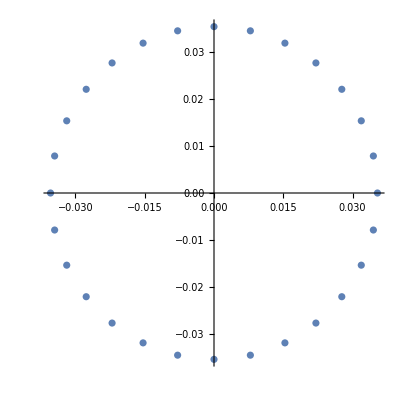

```mathematica
ComplexListPlot[w1]
```

```mathematica
(* mass result below the measured electron mass*)
```

```mathematica
Apply[Plus,Abs[w1]]
```

```mathematica
(*finding the lepton radius scale and next Lepton mass*)
```

```mathematica
mev=0.510998928
```

0.510999

```mathematica
mmu=105.6583715*me/mev
```

1.88353×10^-25

```mathematica
Apply[Plus,Abs[w/.r->μ]]
```

(4.33643×10^-37)/Abs[μ]

```mathematica
rμ=μ/.Solve[(4.336426597595512*^-37)/Abs[μ]==mmu,μ][[2]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

2.30229×10^-12

```mathematica
mtau=1776.82*me/mev;
```

```mathematica
ma=Apply[Plus,Abs[w/.r->τ]]
```

(4.33643×10^-37)/Abs[τ]

```mathematica
rτ=τ/.Solve[ma==mtau,τ][[2]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

1.36905×10^-13

```mathematica
wl=Log[{e,rμ,rτ}/e]
```

{0.,-5.34055,-8.16292}

```mathematica
f[x_]=Fit[wl,{1,x},x]
```

3.66176-4.08146 x

```mathematica
Exp[f[4]]*e
```

1.51912×10^-15

```mathematica
Table[2*Pi*hbar/((Exp[f[i]]*e)*c),{i,-10,10}]
```

{2.22363×10^-47,1.3171×10^-45,7.80142×10^-44,4.62093×10^-42,2.73707×10^-40,1.62122×10^-38,9.60279×10^-37,5.68792×10^-35,3.36906×10^-33,1.99556×10^-31,1.18201×10^-29,7.00126×10^-28,4.14698×10^-26,2.45634×10^-24,1.45494×10^-22,8.61787×10^-21,5.10453×10^-19,3.02351×10^-17,1.79088×10^-15,1.06077×10^-13,6.28317×10^-12}

```mathematica
(*Next Lepton predicted by Log linear scaling of radius:mϕ=1.4549364652443963*^-22gm*)
```

```mathematica
mhiggs=125.38*10^3*me/mev;
```

```mathematica
1.4549364652443963*^-22/(Log[2]*mhiggs)
```

0.939121

```mathematica
(*end*)
```